## Problem 3

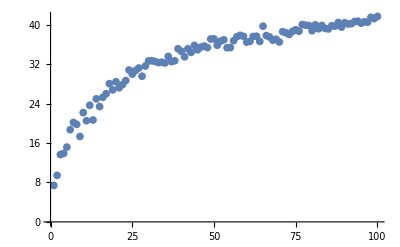

```mathematica
ClearAll["Global`*"]
ϵ=.1;
f[{x__}]:= {x}.Q.{x}
gradf[{x__}]:= {x}.Q
iterationMeans = {};

Do[
iterations = {};

Do[
x = RandomReal[{-10, 10}, n];
Q = DiagonalMatrix[RandomReal[{.5, 1.9}, n]];

gradfx = gradf[x];
iteration = 0;

While[Norm[gradfx]>ϵ,
x += -gradfx;
gradfx = gradf[x];
iteration++;
];
AppendTo[iterations, iteration];
,{ii, 100}];

AppendTo[iterationMeans,Mean[iterations]];
, {n, 100}];
ListPlot[iterationMeans]
```

## Problem 4

```mathematica
ClearAll["Global`*"]
Derive2[f_, {x__}] :=D[D[f[{x}], {{x}}], {{x}}]

f[{x__}]:={x}[[1]]^2+α*{x}[[2]]^2
Derive2[f, {x1, x2}]
```

{{2,0},{0,2 α}}

## Problem 5

```mathematica
ClearAll["Global`*"]
Derive[f_, {x__}] :=D[f[{x}], {{x}}]
Derive2[f_, {x__}] :=D[D[f[{x}], {{x}}], {{x}}]

f1[{x__}]:= ({x}[[1]]-a)^2 + ({x}[[1]]-a)*({x}[[2]]-b) + ({x}[[2]]-b)^2

Simplify[{c, d} - Inverse[Derive2[f1, {c, d}]].Derive[f1, {c, d}]]
```

{a,b}

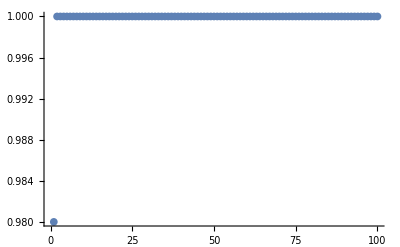

```mathematica
ϵ=.1;
f[{x__}]:= {x}.Q.{x}
gradf[{x__}]:= {x}.Q
iterationMeans = {};

Do[
iterations = {};

Do[
x = RandomReal[{-10, 10}, n];
Q = DiagonalMatrix[RandomReal[{.5, 1.9}, n]];
d2finv = Inverse[Q];
gradfx = gradf[x];
iteration = 0;

While[Norm[gradfx]>ϵ,
x += -d2finv.gradfx;
gradfx = gradf[x];
iteration++;
];
AppendTo[iterations, iteration];
,{ii, 100}];

AppendTo[iterationMeans,Mean[iterations]];
, {n, 100}];
ListPlot[iterationMeans]
```